# one leg model

```mathematica
ClearAll["Global`*"]
ClearAll[Derivative]
```

1

(2 π)/3

NDSolve::svnder: The variables {NDSolve`y$1'} in y''[t]→-g cannot be set as state variables while solving as an ODE because some are the highest order derivatives. You may be able to use these if you solve as a system of DAEs by using Method->{"EquationSimplification"->"Residual"}.

NDSolve::svnder: The variables {NDSolve`x$1'} in x''[t]→0 cannot be set as state variables while solving as an ODE because some are the highest order derivatives. You may be able to use these if you solve as a system of DAEs by using Method->{"EquationSimplification"->"Residual"}.

NDSolve::nbnum1: The function value 0.866025==0.866025[0] is not True or False when the arguments are {0.,-0.5,5.,0.866025,-1.,5.,-2.498×10^-14,-1.,-9.8}.

NDSolve::nbnum1: The function value 0.865021==0.865021[0] is not True or False when the arguments are {0.001,-0.495,4.99981,0.865021,-1.00947,4.99981,-0.375795,-1.00947,-9.14329}.

NDSolve::nbnum1: The function value 0.864007==0.864007[0] is not True or False when the arguments are {0.002,-0.490001,4.99925,0.864007,-1.01829,4.99925,-0.745731,-1.01829,-8.48507}.

General::stop: Further output of NDSolve::nbnum1 will be suppressed during this calculation.

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…]}}

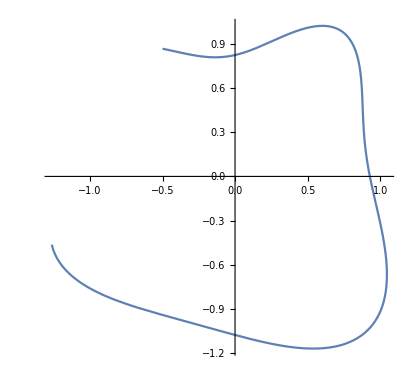

```mathematica
l=1
α=π/2+π/6
x0=l Cos[α];
y0=l Sin[α];

g=9.8;
vx=5;
vy=-1;
ω=15;


sol1=NDSolve[{x''[t]==x [t] ω^2(l/(√(x[t]^2+y[t]^2))-1),y''[t]==y[t] ω^2(l/(√(x[t]^2+y[t]^2))-1)-g,x'[0]==vx,y'[0]==vy,x[0]==x0,y[0]==y0,WhenEvent[y[t]==y[0],{y''[t]->-g,x''[t]->0}]},{x,y},{t,0,3},StartingStepSize->0.001, Method->{"FixedStep",Method->{"ExplicitRungeKutta","DifferenceOrder"->4}}]
ParametricPlot[Evaluate[{x[t],y[t]}/.sol1],{t,0,1},PlotRange->All]
```

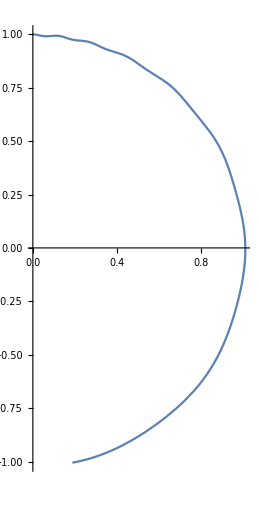

```mathematica
^
```